## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulum.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-B/C-inplementazioa/Packages/

```mathematica
Get["NBodyProblem`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Orange;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Yellow;
StyleError=Lighter[Blue,.6];
StyleEstimation=Orange;
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<>DataDirectory<>"outC.bin";
fileD=NotebookDirectory[]<>DataDirectory<>"outD.bin";
fileE=NotebookDirectory[]<>DataDirectory<>"outE.txt";
```

### Output Files

```mathematica
esperiment="NBODY";

(* energy error*)
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3A.pdf";
plot1b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3B.pdf";
plot2=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot2.pdf";
plot11=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot11.pdf";
plot12=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot12.pdf";
plot13=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot13.pdf";
(*Global errors*)
plot3=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"4A.pdf";
plot3b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"4B.pdf";
(* distribution of energy jumps*)
plot4=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2A.pdf";
plot5=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2B.pdf";
plot5D=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot5D.pdf";
(* error estimation*)
plot6=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"5B.pdf";
plot6a=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"5A.pdf"; 
plot7=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot7.pdf";
```

```mathematica
plot21=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot21.pdf";
plot22=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot22.pdf";
plot23=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot23.pdf";
```

## Parameters (N6-Body Problem)

### Problem parameters and initial values (Hairer)

```mathematica
prec=100;
n=6;
neq=36;
```

```mathematica
q={0.,0.,0.,
-3.5023653,-3.8169847,-1.5507963,
9.0755314,-3.0458353,-1.6483708,
8.3101420,-16.2901086,-7.2521278,
11.4707666,-25.7294829,-10.8169456,
-15.5387357,-25.2225594,-3.1902382};

v={0.,0.,0.,
0.00565429,-0.00412490,-0.00190589,
0.00168318,0.00483525,0.00192462,
0.00354178,0.00137102,0.00055029,
0.00288930,0.00114527,0.00039677,
0.00276725,-0.00170702,-0.00136504};
```

```mathematica
u=Flatten[{q,v}];
```

```mathematica
G=2.95912208286*10^-4;
m[1]=1.00000597682;
m[2]=0.000954786104043;
m[3]=0.000285583733151;
m[4]=0.0000437273164546;
m[5]=0.0000517759138449;
m[6]=1.0/(1.3*10^8);
Gm=Table[G*m[i],{i,1,n}];
(* sun, Jupiter, Saturn, Uranus, Neptune, Pluto *)
```

```mathematica
orderplanets= Sort[Range[n],Abs[Gm[[#1]]]< Abs[Gm[[#2]]]&]-1
```

{5,3,4,2,1,0}

```mathematica
preal=parameters=Gm;
pint=orderplanets;
```

```mathematica
u0=Chdata[u,preal];
u0D=N[u0];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;
```

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
N[ee0,20]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### Integration parameters.

```mathematica
h=500./3;
t0=0.;tend=h*60000;(*h*60000*)
(*tend=1000.;*)
(*tend=h*10;*)

sampling=120;(*120*)
(*sampling=10;*)
(*sampling=2^3;*)
(*sampling=1;*)
```

```mathematica
codfun0=2; (*NBody Problem*)
codfunX=12; (*NBody ProblemX*)
ns= 6;
nstep=(tend-t0)/h
nout=nstep/sampling
```

1800.

225.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=NBodyHam;
HAM2=NBodyHam3;
MOM=NBodyMom;
ERR=ErrorPosition;
```

## Import

```mathematica
Now
```

Fri 6 Jan 2017 10:27:40GMT+1.

```mathematica
nstat=1;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
noutB=noutC=noutD=noutE=noutA;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real128"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1,226}

```mathematica
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real128"],{nstat,noutB,dd1}],prec];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpB=Map[First,Partition[tpB,step]];
{Length[outB],Length[outB[[1]]]}
```

{1,226}

```mathematica
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutC,dd2}],prec];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
tpC=Map[First,Partition[tpC,step]];
{Length[outC],Length[outC[[1]]]}
```

{1,226}

```mathematica
outD=SetPrecision[ArrayReshape[BinaryReadList[fileD,"Real64"],{nstat,noutD,dd1}],prec];
tpD=Flatten[Take[outD[[1]],All,{1,1}]];
tpD=Map[First,Partition[tpD,step]];
{Length[outD],Length[outD[[1]]]}
```

{1,226}

```mathematica
outE=SetPrecision[ArrayReshape[Import[fileE,"Data"],{nstat,noutE,dd3}],prec];
tpE=Flatten[Take[outE[[1]],All,{1,1}]];
tpE=Map[First,Partition[tpE,step]];
{Length[outE],Length[outE[[1]]]}
```

Import::nffil: File not found during Import.

ArrayReshape::list: The specified argument $Failed should be a list or a SparseArray.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,All,{1,1}].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

First::normal: Nonatomic expression expected at position 1 in First[All].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[First[$Failed],First[All],1].

{2,0}

## Analisis-I

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, preal,neq,prec,step] ;
{MeanHamB,DesvHamB}=FunEnergy [outB, nstat,noutA,HAM,preal,neq,prec,step] ;
{MeanHamC,DesvHamC}=FunEnergy[outC, nstat,noutA,HAM, preal,neq,prec,step] ;
{MeanHamD,DesvHamD}=FunEnergy[outD, nstat,noutA,HAM, preal,neq,prec,step] ;
```

```mathematica
(*LimitErr=10^(-12);
{MeanHamE,DesvHamE}=FunEnergyFortran[outE,nstat,noutE,HAM2,preal,neq,prec,step,LimitErr];*)
MeanHamE=Partition[Array[0. &,noutE*dd3],dd3];
DesvHamE=Partition[Array[0. &,noutE*dd3],dd3];
tpE=tpB;
```

#### Plot (1)

```mathematica
eskala=10^(15);
(*eskala=1;*)
x0=0;
x1=tend;
y0=-1.5;
y1=1.5;
```

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA*eskala}];
MeanHamBdata = Transpose[{tpB,MeanHamB*eskala}];
MeanHamCdata = Transpose[{tpC,MeanHamC*eskala}];
MeanHamDdata = Transpose[{tpD,MeanHamD*eskala}];
MeanHamEdata = Transpose[{tpE,MeanHamE*eskala}];

DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
DesvHamBdata = Transpose[{tpB,DesvHamB*eskala}];
DesvHamCdata = Transpose[{tpC,DesvHamC*eskala}];
DesvHamDdata = Transpose[{tpD,DesvHamD*eskala}];
DesvHamEdata = Transpose[{tpE,DesvHamE*eskala}];
```

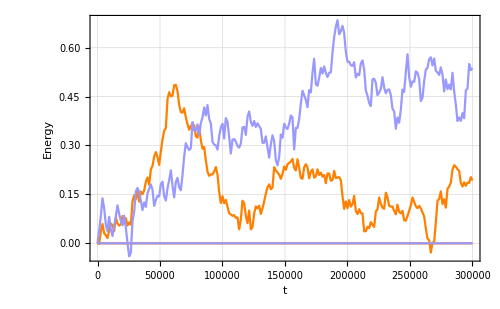

```mathematica
plot=ListPlot[{MeanHamBdata,MeanHamCdata,MeanHamEdata,DesvHamBdata,DesvHamCdata,DesvHamEdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
(*PlotLegends->Placed[{"FPIEA","DP","Hairer"(*,"standard deviation"*)},Below],*)
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1,Show[plot] ];
```

#### Plot (1b) (* mean detail*)

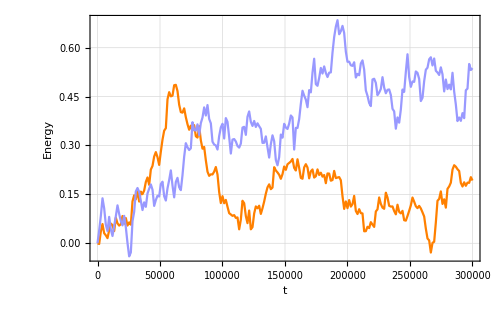

```mathematica
plot=ListPlot[{MeanHamBdata,MeanHamCdata,(*MeanHamEdata*)},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
(*PlotLegends->Placed[{"FPIEA","DP"(*,"Hairer"*)(*,"standard deviation"*)},Below],*)
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1b,Show[plot] ];
```

#### Alpha*Sqrt[n]

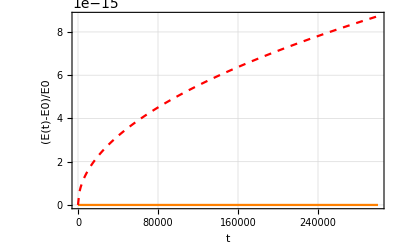

```mathematica
alphaB=2^(-55.8);
HamBdataT12=Transpose[{tpA,FunT12[alphaB,tpB]}];
plot=ListPlot[{DesvHamBdata,HamBdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

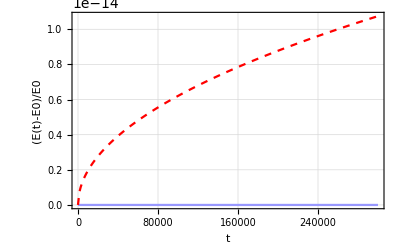

```mathematica
alphaC=2^(-55.5);
HamCdataT12=Transpose[{tpC,FunT12[alphaC,tpC]}];
plot=ListPlot[{DesvHamCdata,HamCdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{(*StyleIdeal,*)StyleMachine,(*StyleClassic,*)StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

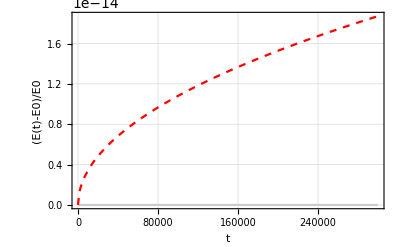

```mathematica
alphaD=2^(-54.7);
HamDdataT12=Transpose[{tpD,FunT12[alphaD,tpD]}];
plot=ListPlot[{DesvHamDdata,HamDdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{(*StyleIdeal,StyleMachine,*)StyleClassic,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

#### Plot (2)

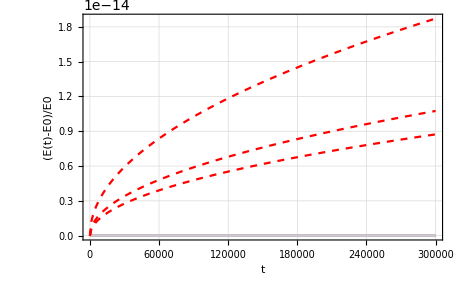

```mathematica
plot=ListPlot[{DesvHamBdata,DesvHamCdata,DesvHamDdata,
                             HamBdataT12,HamCdataT12,HamDdataT12},AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic,
                       StyleHamT12,StyleHamT12,StyleHamT12},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot2,Show[plot] ];
```

### Graphics-I (Energy-2): Plot11,Plot12,Plot13

```mathematica
maxnstat=100;
If[nstat<maxnstat,nstat0=nstat,nstat0=maxnstat];
```

```mathematica
AllHamerrB=FunAllEnergy[outB, nstat0,noutA,HAM, parameters,neq,prec,step] ;
AllHamerrC=FunAllEnergy[outC, nstat0,noutA,HAM, parameters,neq,prec,step] ;
AllHamerrD=FunAllEnergy[outD, nstat0,noutA,HAM, parameters,neq,prec,step] ;
```

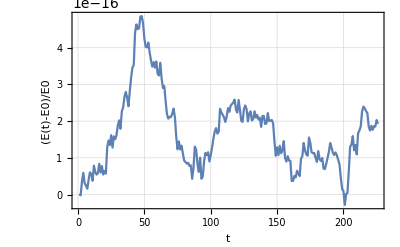

```mathematica
plot=ListPlot[Table[AllHamerrB[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot11,Show[plot] ];
```

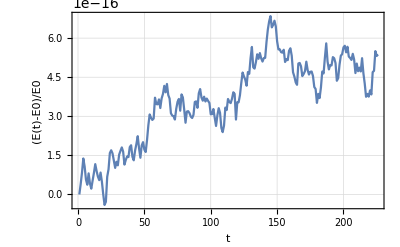

```mathematica
plot=ListPlot[Table[AllHamerrC[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot12,Show[plot] ];
```

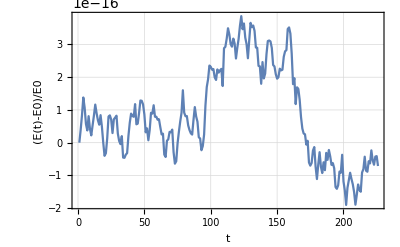

```mathematica
plot=ListPlot[Table[AllHamerrD[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot13,Show[plot] ];
```

### Graphics-II (Global Error): Plot3

```mathematica
{MeanErrA,DesvErrA}=FunErrorNEW[outA, outA,ERR, nstat,noutA,neq,prec,step];
{MeanErrB,DesvErrB}=FunErrorNEW[outA, outB,ERR, nstat,noutA,neq,prec,step];
{MeanErrC,DesvErrC}=FunErrorNEW[outA, outC,ERR, nstat,noutA,neq,prec,step];
{MeanErrD,DesvErrD}=FunErrorNEW[outA, outD,ERR, nstat,noutA,neq,prec,step];
```

```mathematica
MeanErrBdata = Transpose[{tpB,MeanErrB}];
MeanErrCdata = Transpose[{tpC,MeanErrC}];
MeanErrDdata = Transpose[{tpD,MeanErrD}];
```

```mathematica
DesvErrBdata = Transpose[{tpB,DesvErrB}];
DesvErrCdata = Transpose[{tpC,DesvErrC}];
DesvErrDdata = Transpose[{tpD,DesvErrD}];
```

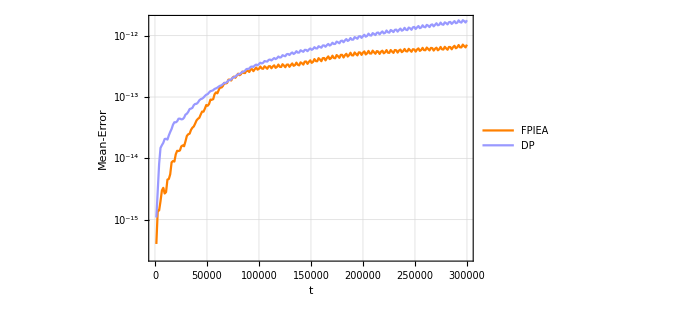

```mathematica
plot=ListLogPlot[{MeanErrBdata,MeanErrCdata},
AxesLabel->{"t","Mean-Error"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"FPIEA","DP"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Mean-Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot3,Show[plot] ];
```

```mathematica
plot=ListLogPlot[{DesvErrBdata,DesvErrCdata},
AxesLabel->{"t","Desv-Error"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"FPIEA","DP"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Desv-Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot3b,Show[plot] ];
```

-Graphics-

### Graphics-III (Histogram) : Plot4, Plot5

```mathematica
HamerrA=FunHamErrDif[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrB=FunHamErrDif[outB,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrC=FunHamErrDif[outC,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrD=FunHamErrDif[outD,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

#### B-Integration: Plot4

0.00085573360756667109896742940928464464745984382772061312224631078020408809638518684

0.024845182420338032662303056552788809205349874154060690187048452090766642719003131

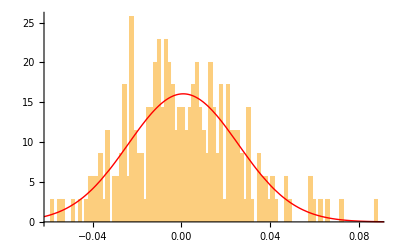

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-B/C-inplementazioa/Experiments/7-6-Body  (p=1000, approx=0) /Images/NBODY2A.pdf

```mathematica
Hamerdif=HamerrB 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot4,Show[ir1,ir2]]
```

```mathematica
Length[Hamerdif]
```

225

#### C-Integration: Plot5

0.0023877432680439496488029921374660262525964810789390143804795293499376498917786428

0.0346107959830030695763920689311399898721494273666748972718660691770280994380183352

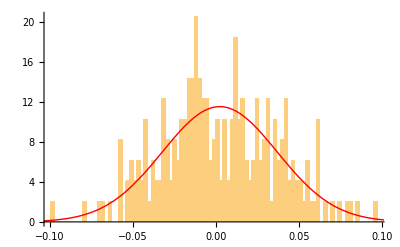

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-B/C-inplementazioa/Experiments/7-6-Body  (p=1000, approx=0) /Images/NBODY2B.pdf

```mathematica
Hamerdif=HamerrC 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot5,Show[ir1,ir2]]
```

#### D-Integration: Plot5

-0.0003166320283137614103820240474577360331810222736783206903373842029478234522841203

0.0356195492713544776244509988827896487117303671550578725325587002773116746581412699

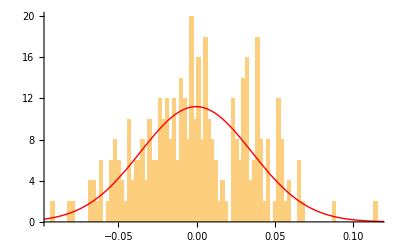

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-B/C-inplementazioa/Experiments/7-6-Body  (p=1000, approx=0) /Images/NBODYplot5D.pdf

```mathematica
Hamerdif=HamerrD 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot5D,Show[ir1,ir2]]
```

### Tables

#### Quadruple

```mathematica
MeanD0=0.; (*(SD0A/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamA]]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrA]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.07742×10^-18,-5.64122×10^-22,3.47919×10^-19,0.}

#### FPIEA

```mathematica
MeanD0=0.;(*(SD0B/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamB]]//N;
Hamerdif=Drop[MeanHamB ,1]-Drop[ MeanHamB,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrB]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,4.86106×10^-16,8.55734×10^-19,2.48452×10^-17,7.15035×10^-13}

#### DP

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamC]]//N;
Hamerdif=Drop[MeanHamC ,1]-Drop[ MeanHamC,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrC]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,6.84475×10^-16,2.38774×10^-18,3.46108×10^-17,1.78963×10^-12}

#### DP-Estandarra

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[Abs[MeanHamD]]//N;
Hamerdif=Drop[MeanHamD ,1]-Drop[ MeanHamD,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrD]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,3.8662×10^-16,-3.16632×10^-19,3.56195×10^-17,6.68462×10^-13}

### Graphics-IV (Angular-Momentum): Plot21, Plot22, Plot23

```mathematica
{MeanLA,DesvLA}=FunMomentum[outA, nstat,noutA,MOM, parameters,neq,prec,step] ;
{MeanLB,DesvLB}=FunMomentum [outB, nstat,noutA,MOM, parameters,neq,prec,step] ;
{MeanLC,DesvLC}=FunMomentum[outC, nstat,noutA,MOM, parameters,neq,prec,step] ;
{MeanLD,DesvLD}=FunMomentum[outD, nstat,noutA,MOM, parameters,neq,prec,step] ;
```

#### Plot21, Plot22, Plot23

```mathematica
MeanLAdata=Array[0 &,3];
MeanLBdata=Array[0 &,3];
MeanLCdata=Array[0 &,3];
MeanLDdata=Array[0 &,3];
DesvLAdata=Array[0 &,3];
DesvLBdata=Array[0 &,3];
DesvLCdata=Array[0 &,3];
DesvLDdata=Array[0 &,3];
```

```mathematica
Do[MeanLAdata[[i]] = Transpose[{tpA,MeanLA[[All,i]]}],{i,3}];
Do[MeanLBdata[[i]] = Transpose[{tpB,MeanLB[[All,i]]}],{i,3}];
Do[MeanLCdata[[i]] = Transpose[{tpC,MeanLC[[All,i]]}],{i,3}];
Do[MeanLDdata[[i]] = Transpose[{tpD,MeanLD[[All,i]]}],{i,3}];
Do[DesvLAdata[[i]] = Transpose[{tpA,DesvLA[[All,i]]}],{i,3}];
Do[DesvLBdata[[i]] = Transpose[{tpB,DesvLB[[All,i]]}],{i,3}];
Do[DesvLCdata[[i]] = Transpose[{tpC,DesvLC[[All,i]]}],{i,3}];
Do[DesvLDdata[[i]] = Transpose[{tpD,DesvLD[[All,i]]}],{i,3}];
```

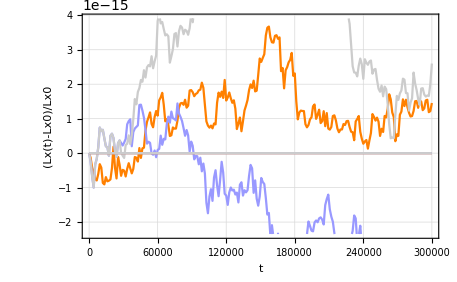

```mathematica
i=1;
plot=ListPlot[{MeanLBdata[[i]],MeanLCdata[[i]],MeanLDdata[[i]],DesvLBdata[[i]],DesvLCdata[[i]],DesvLDdata[[i]]},AxesLabel->{"t","(Lx(t)-Lx0)/Lx0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic,StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(Lx(t)-Lx0)/Lx0"}]
Export[plot21,Show[plot] ];
```

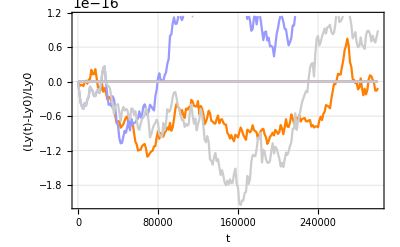

```mathematica
i=2;
plot=ListPlot[{MeanLBdata[[i]],MeanLCdata[[i]],MeanLDdata[[i]],DesvLBdata[[i]],DesvLCdata[[i]],DesvLDdata[[i]]},AxesLabel->{"t","(Ly(t)-Ly0)/Ly0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic,StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(Ly(t)-Ly0)/Ly0"}]
Export[plot22,Show[plot] ];
```

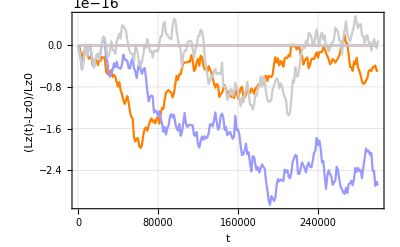

```mathematica
i=3;
plot=ListPlot[{MeanLBdata[[i]],MeanLCdata[[i]],MeanLDdata[[i]],DesvLBdata[[i]],DesvLCdata[[i]],DesvLDdata[[i]]},AxesLabel->{"t","(Lz(t)-Lz0)/Lz0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic,StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","(Lz(t)-Lz0)/Lz0"}]
Export[plot23,Show[plot] ];
```

## Analisis-II: error estimation

```mathematica
Now
```

Fri 6 Jan 2017 10:28:18GMT+1.

### Estimation: Plot6

```mathematica
tp=tpC;
{MeanEst,DesvEst,MeanQty,DesvQty}=FunEstimation[outA,outC,ERR,nstat,noutA,neq,prec,step];
MeanEstdata = Transpose[{tp,MeanEst}];
Desvdata1=Transpose[{tp,MeanEst+DesvEst}];
Desvdata2=Transpose[{tp,MeanEst-DesvEst}];
```

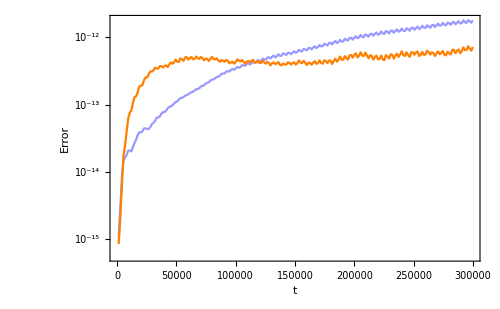

```mathematica
MeanErrdata=MeanErrCdata;
plot=ListLogPlot[{Abs[MeanErrdata ],Abs[MeanEstdata]},
AxesLabel->{"t","Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
(*PlotLegends->Placed[{"Errorrea","Estimazioa"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot6,Show[plot]];
```

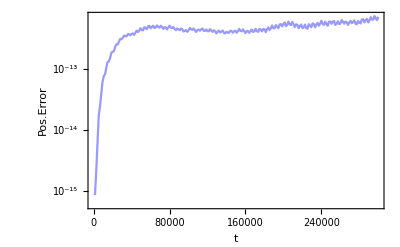

```mathematica
plot=ListLogPlot[{(*Abs[MeanErrCdata],*)Abs[MeanEstdata]},AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

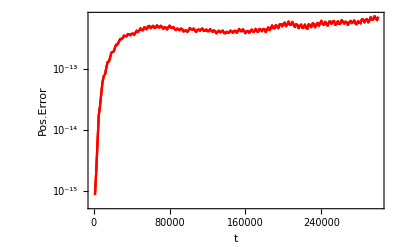

```mathematica
plot6b=ListLogPlot[{ MeanEstdata, Desvdata1,Desvdata2},
AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{Orange,Red,Red},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

### Estimation: Plot6a (bakarra)

```mathematica
tp=tpC;
mynstat=1;
{MeanEst,DesvEst,MeanQty,DesvQty}=FunEstimation[outA,outC,ERR,mynstat,noutA,neq,prec,step];
MeanEstdata = Transpose[{tp,MeanEst}];
Desvdata1=Transpose[{tp,MeanEst+DesvEst}];
Desvdata2=Transpose[{tp,MeanEst-DesvEst}];
```

```mathematica
MeanErrdata=MeanErrCdata;
plot=ListLogPlot[{Abs[MeanErrdata ],Abs[MeanEstdata]},
AxesLabel->{"t","Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
(*PlotLegends->Placed[{"Errorrea","Estimazioa"},Below],*)
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot6a,Show[plot]];
```

-Graphics-

### Quality estimation: Plot7

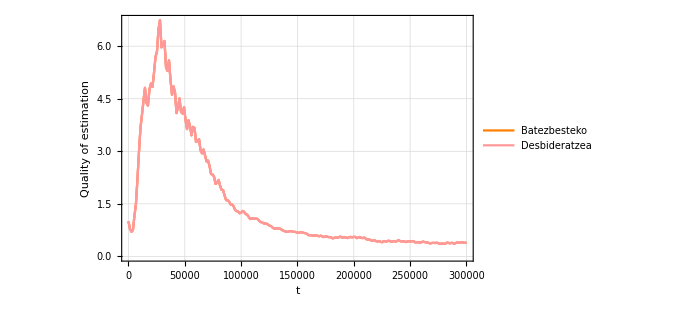

```mathematica
MeanQtydata=Transpose[{tpC,10^MeanQty}];
MeanQtyData1=Transpose[{tpC,10^(MeanQty+DesvQty)}];
MeanQtyData2=Transpose[{tpC,10^(MeanQty-DesvQty)}];
plot=ListPlot[{MeanQtydata,MeanQtyData1,MeanQtyData2},
AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotLegends->Placed[{"Batezbesteko","Desbideratzea"},Below],
PlotRange->All,
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleEstimation,Lighter[Red,.6],Lighter[Red,.6]},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Quality of estimation"},
LabelStyle->Directive[Black,Bold]
]
Export[plot7,Show[plot]];
```

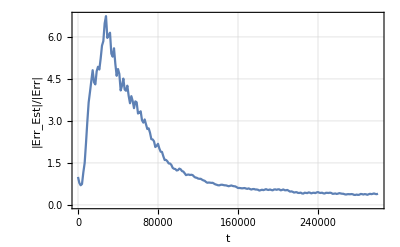

```mathematica
plot=ListPlot[{MeanQtydata},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","|Err_Est|/|Err|"}]
```